## Initialize some functions

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PerformanceGoal->"Quality",PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
exportOptions={"AllowRasterization"->True,ImageResolution->800};
plotOptions={Frame->True,PerformanceGoal->"Quality",Evaluate@font,Axes->False};
```

```mathematica
density1={Evaluate@font,ColorFunction->"SunsetColors"};
density2={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",PlotLegends->True,ImageSize->310};
density3={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",PlotLegends->True,ImageSize->410};
export1={"AllowRasterization"->True,ImageResolution->800};
plot1={Frame->True,Evaluate@font,Axes->False};
plot2={Frame->True,PerformanceGoal->"Quality",ImageSize->310,Evaluate@font,Axes->False,PlotStyle->Thickness[0.004]};
```

## Defining the Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
as={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

## Printing functions

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

# N = 1

```mathematica
nn=1;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{λ,χ},Evaluate@HH,Evaluate@compileOptions]
```

{{-1/2-λ/4,-χ/2},{-χ/2,1/2-λ/4-χ^2}}

CompiledFunction[…]

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-1/2-λ/4 | -χ/2
-χ/2 | 1/2-λ/4-χ^2)

## Energies and eigenvalues

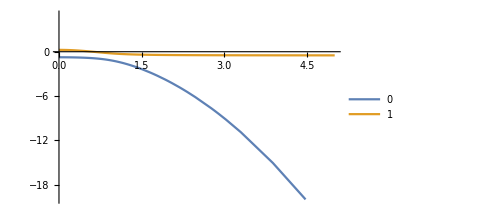
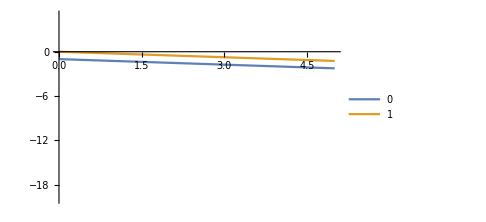

```mathematica
energies1=Eigenvalues[H[1,χ]];
energies2=Eigenvalues[H[λ,1]];
plotOpt={PlotLegends->Range[0,nn],PlotPoints->10,PlotRange->{Automatic,{-20,5}},Evaluate@font,ImageSize->Medium};
{Plot[energies1,{χ,0,5},Evaluate@plotOpt],
Plot[energies2,{λ,0,5},Evaluate@plotOpt]}
```

## Metric tensor

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors},
energies=Eigenvalues[H[λ,χ]];
eigenvectors=Map[Normalize,Eigenvectors[H[λ,χ]]];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
FullSimplify[{{g11,g12},{g12,g22}}]
]
```

```mathematica
g[λ,χ][[2,2]]/.χ->χ[t]
```

((1+χ[t]^2)^2)/(4 (1-χ[t]^2+χ[t]^4)^2)

```mathematica
dsol=DSolve[{((1+χ[τ]^2)^2)/(4 (1-χ[τ]^2+χ[τ]^4)^2)χ'[τ]^2==1,χ[τf]==χf},χ[τ],τ,Assumptions->{χ>0,χi>0,χf>0,τf>0,λ∈Reals}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

$Aborted

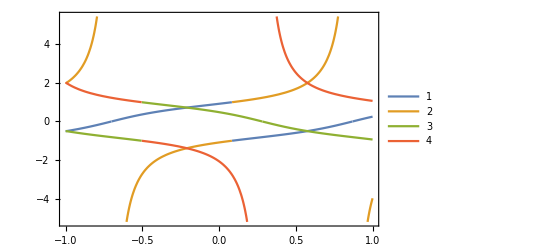

```mathematica
Plot[Evaluate[(χ[τ]/.dsol)/.{χf->2,τf->10}],{τ,-1,1},PlotLegends->Automatic,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"\\tau","\\chi"}]
```

# N = 2

```mathematica
nn=2;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{λ,χ},Evaluate@HH,Evaluate@compileOptions]
```

{{-1-λ/4,-χ/(2 √2),-λ/4},{-χ/(2 √2),1/2 (-λ-χ^2),-1/2 (1/(√2)+√2) χ},{-λ/4,-1/2 (1/(√2)+√2) χ,1+1/2 (-λ/2-4 χ^2)}}

CompiledFunction[…]

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-1-λ/4 | -χ/(2 √2) | -λ/4
-χ/(2 √2) | -λ/2-χ^2/2 | -(3 χ)/(2 √2)
-λ/4 | -(3 χ)/(2 √2) | 1-λ/4-2 χ^2)

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig[[1]]].DH1C[λ,χ].eig[[#]]&/@Range[2,dim];
M1T=Conjugate[eig[[#]]].DH1C[λ,χ].eig[[1]]&/@Range[2,dim];
M2=Conjugate[eig[[1]]].DH2C[λ,χ].eig[[#]]&/@Range[2,dim];
M2T=Conjugate[eig[[#]]].DH2C[λ,χ].eig[[1]]&/@Range[2,dim];
endif=(en[[1]]-en[[#]])^2&/@Range[2,dim];
g11=Re@Sum[(M1[[i]]M1T[[i]])/endif[[i]],{i,1,dim-1}];
g12=Re@Sum[(M1[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
g22=Re@Sum[(M2[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

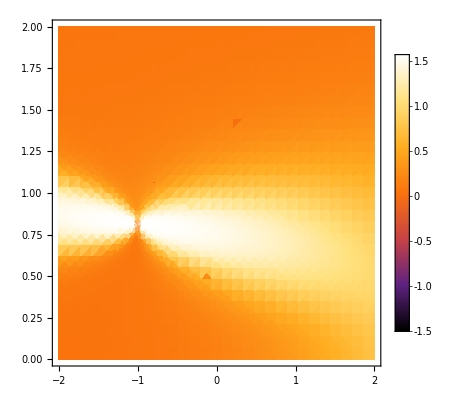

```mathematica
DensityPlot[ArcTan@gC[λ,χ],{λ,-2,2},{χ,0,2},Evaluate@densityPlotOptions,PlotPoints->30]
```

## Energies and eigenvalues

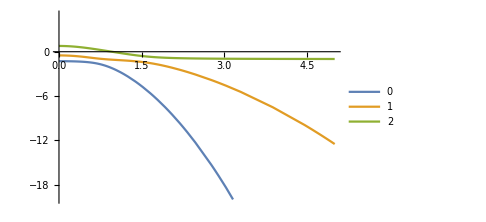
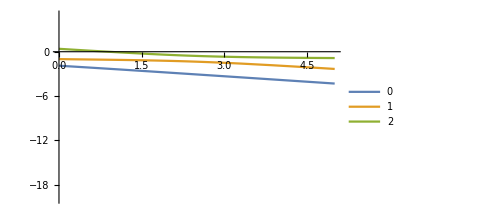

```mathematica
energies1=Eigenvalues[H[1,χ]];
energies2=Eigenvalues[H[λ,1]];
plotOpt={PlotLegends->Range[0,nn],PlotPoints->10,PlotRange->{Automatic,{-20,5}},Evaluate@font,ImageSize->Medium};
{Plot[energies1,{χ,0,5},Evaluate@plotOpt],
Plot[energies2,{λ,0,5},Evaluate@plotOpt]}
```

Analytical formula for energies Eigenvalues[H[λ,χ],Cubics→True] can be rewritten using some substitution, because of rounding errors (order of numerical precision 10^-16)

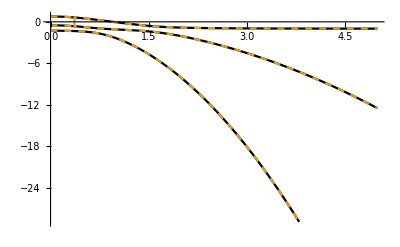

```mathematica
enA[λ_,χ_]:=2^(2/3)(2 λ (18+λ^2)-3 (-48+λ (45+λ)) χ^2+3 (-9+11 λ) χ^4-70 χ^6+√(-4 enD[λ,χ]^3+(2 λ (18+λ^2)-3 (-48+λ (45+λ)) χ^2+3 (-9+11 λ) χ^4-70 χ^6)^2))^(1/3);
enB[λ_,χ_]:=4 (2 λ+5 χ^2);
enD[λ_,χ_]:=(12+λ^2-(9+λ) χ^2+13 χ^4);
enSim[λ_,χ_]:=1/24 { 
(- enB[λ,χ]-(8 (-1)^(1/3) enD[λ,χ])/enA[λ,χ]+(-1+ⅈ √3) enA[λ,χ]), 
(- enB[λ,χ]+(8 (-1)^(2/3) enD[λ,χ])/enA[λ,χ]-(1+ⅈ √3) enA[λ,χ]),
(- enB[λ,χ]+(8enD[λ,χ])/enA[λ,χ]+2  enA[λ,χ])}
Plot[{Re@enSim[1,χ],Eigenvalues[H[1,χ]]},{χ,0,5},PlotStyle->{Black,Dashed}]
```

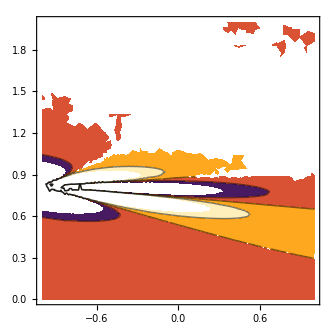

```mathematica
ContourPlot[Evaluate@D[enSim[λ,χ]⟦1⟧,{χ,2},{λ,2}],{λ,-1,1},{χ,0,2},ImageSize->Large,ColorFunction->"SunsetColors",PlotPoints->10]
```

```mathematica
dens=DensityPlot[Det@gC[λ,χ],{λ,-1,20},{χ,0,2},ImageSize->Large,ColorFunction->"SunsetColors",PlotPoints->15,ScalingFunctions->"Log"];
```

```mathematica
DenSim1[λ_,χ_]=D[enSim[λ,χ]⟦1⟧-enSim[λ,χ]⟦2⟧,{χ,1},{λ,1}];
```

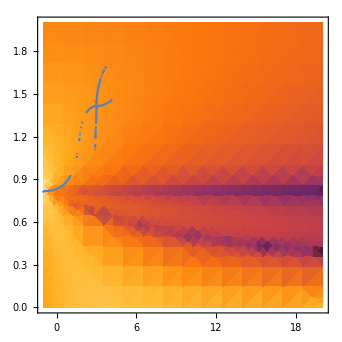

```mathematica
cont=ContourPlot[DenSim1[λ,χ]==0,{λ,-1,20},{χ,0,2},ImageSize->Large,PlotPoints->25];
Show[dens,cont]
```

## Metric tensor

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors},
g11=Re@Sum[((Conjugate[eigenVec[λ,χ][[1]]].DH1[λ,χ].eigenVec[λ,χ][[i]])(Conjugate[eigenVec[λ,χ][[i]]].DH1[λ,χ].eigenVec[λ,χ][[1]]))/(enSim[λ,χ][[1]]-enSim[λ,χ][[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenVec[λ,χ][[1]]].DH1[λ,χ].eigenVec[λ,χ][[i]]Conjugate[eigenVec[λ,χ][[i]]].DH2[λ,χ].eigenVec[λ,χ][[1]])/(enSim[λ,χ][[1]]-enSim[λ,χ][[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenVec[λ,χ][[1]]].DH2[λ,χ].eigenVec[λ,χ][[i]])(Conjugate[eigenVec[λ,χ][[i]]].DH2[λ,χ].eigenVec[λ,χ][[1]]))/(enSim[λ,χ][[1]]-enSim[λ,χ][[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
N@g[3,5]
N@g[-1,-1]
```

{{0.0000273694,-0.0000780008},{-0.0000780008,0.000997044}}

{{0.12963,0.0555556},{0.0555556,0.222222}}

# N = 3

## Defining the Hamiltonian

```mathematica
nn=3;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

{{-3/2-λ/4,-χ/(2 √3),-λ/(2 √3),0},{-χ/(2 √3),-1/2+1/3 (-(7 λ)/4-χ^2),-χ,-λ/(2 √3)},{-λ/(2 √3),-χ,1/2+1/3 (-(7 λ)/4-4 χ^2),-(5 χ)/(2 √3)},{0,-λ/(2 √3),-(5 χ)/(2 √3),3/2+1/3 (-(3 λ)/4-9 χ^2)}}

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(1/4 (-6-λ) | -χ/(2 √3) | -λ/(2 √3) | 0
-χ/(2 √3) | 1/12 (-6-7 λ-4 χ^2) | -χ | -λ/(2 √3)
-λ/(2 √3) | -χ | 1/12 (6-7 λ-16 χ^2) | -(5 χ)/(2 √3)
0 | -λ/(2 √3) | -(5 χ)/(2 √3) | 3/2-λ/4-3 χ^2)

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig[[1]]].DH1C[λ,χ].eig[[#]]&/@Range[2,dim];
M1T=Conjugate[eig[[#]]].DH1C[λ,χ].eig[[1]]&/@Range[2,dim];
M2=Conjugate[eig[[1]]].DH2C[λ,χ].eig[[#]]&/@Range[2,dim];
M2T=Conjugate[eig[[#]]].DH2C[λ,χ].eig[[1]]&/@Range[2,dim];
endif=(en[[1]]-en[[#]])^2&/@Range[2,dim];
g11=Re@Sum[(M1[[i]]M1T[[i]])/endif[[i]],{i,1,dim-1}];
g12=Re@Sum[(M1[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
g22=Re@Sum[(M2[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

## Energies and eigenvalues

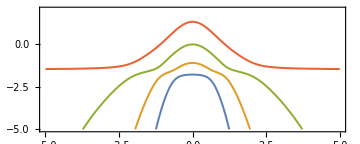
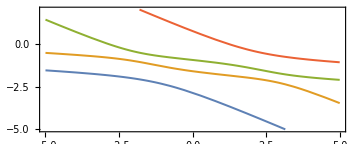

```mathematica
energies1=Eigenvalues[H[1,χ]];
energies2=Eigenvalues[H[λ,1]];
plotOpt={PlotPoints->20,PlotRange->{Automatic,{-5,2}},Evaluate@font,ImageSize->Medium,Frame->True,Axes->False,PerformanceGoal->"Quality",PlotStyle->Thickness[0.004],AspectRatio->0.4};
{plA,plB}={Plot[energies1,{χ,-5,5},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\chi","E /Ry"}],
Plot[energies2,{λ,-5,5},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\lambda","E /Ry"}]}
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_energiesl.pdf",plA,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"../dp_text/img/N=3_energiesc.pdf",plB,"AllowRasterization"->True,ImageResolution->800];
```

Analytical formula for energies Eigenvalues[H[λ,χ],Cubics→True] can be rewritten using some substitution, because of rounding errors (order of numerical precision 10^-16)

```mathematica
en[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort@enNonSort
]
```

```mathematica
points=
enDifPlot=Show[{
DensityPlot[(#⟦4⟧-#⟦1⟧)&/@{ND[en[λ,c],c,χ]},{λ,-0.55,-0.45},{χ,0.7,0.9},Evaluate@densityPlotOptions,PlotPoints->150, ImageSize->310],
ListPlot[{{-1/2,Sqrt[3/5]},{-1/2,-Sqrt[3/5]}},PlotStyle->Green]
}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_en4-en1.pdf",enDifPlot,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
FindMinimum[Flatten@{(#⟦4⟧-#⟦1⟧)&/@{en[λ,χ]},-1<λ<0,0<χ<1},{λ,-0.55},{χ,0.5}]
```

{0.744182,{λ→-4.46254×10^-8,χ→1.}}

```mathematica
NMinimize[{(#⟦4⟧-#⟦1⟧)&/@{en[λ,χ]},-1<λ<0,0<χ<1},{λ,χ}]
```

NMinimize[{{-λ+en[λ,χ]⟦4⟧},-1<λ<0,0<χ<1},{λ,χ}]

```mathematica
enDifPlotd=DensityPlot[(#⟦4⟧-#⟦1⟧)&/@{ND[en[λ,c],c,χ]},{λ,-5,5},{χ,-1.2,1.2},Evaluate@densityPlotOptions,PlotPoints->150, ImageSize->310]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_en4-en1_der.pdf",enDifPlotd,"AllowRasterization"->True,ImageResolution->800];
```

## Energies and eigenvectors analytically

```mathematica
Eigenvalues[H[λ,χ],Quartics->True]
```

```mathematica
enA[λ_,χ_]:=16 2^(1/3) (25515+64 λ^6-108621 χ^2-192 λ^5 χ^2+309096 χ^4-326727 χ^6+162648 χ^8-81855 χ^10+24013 χ^12-8 λ^3 χ^2 (-513+414 χ^2+29 χ^4)+24 λ^4 (36-93 χ^2+52 χ^4)+6 λ χ^2 (16119-42660 χ^2+29691 χ^4-3198 χ^6+409 χ^8)+6 λ^2 (1377-10557 χ^2+17595 χ^4-10053 χ^6+1225 χ^8)+√(-(1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8)^3+(25515+8262 λ^2+864 λ^4+64 λ^6-3 (36207+2 λ (-16119+λ (10557+4 λ (-171+λ (93+8 λ))))) χ^2+6 (51516+λ (-42660+λ (17595+8 λ (-69+26 λ)))) χ^4-(326727+2 λ (-89073+λ (30159+116 λ))) χ^6+6 (27108+λ (-3198+1225 λ)) χ^8+3 (-27285+818 λ) χ^10+24013 χ^12)^2))^(1/3)
enC[λ_,χ_]:=(256 2^(1/3) (1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8))/(3 enA[λ,χ])
enB[λ_,χ_]:=4 √(16/3 (45+4 λ^2-(33+4 λ) χ^2+49 χ^4)+enC[λ,χ]+1/(3 2^(1/3))enA[λ,χ])
enD[λ_,χ_]:=8 (5 λ+14 χ^2)^2-8/3 (-180+59 λ^2+132 χ^2+436 λ χ^2+392 χ^4)-enC[λ,χ]-1/(3 2^(1/3))enA[λ,χ]
enE[λ_,χ_]:=(9216 (λ-4 (-1+λ) χ^2+(-1+λ) χ^4-2 χ^6))/enB[λ,χ]
enF[λ_,χ_]:=1/2 √(16/3 (45+4 λ^2-(33+4 λ) χ^2+49 χ^4)+enC[λ,χ]+1/(3 2^(1/3))enA[λ,χ])
enG[λ_,χ_]:=-5 λ-14 χ^2
```

```mathematica
enSim[λ_,χ_]:=
{1/12 (enG[λ,χ]-enF[λ,χ]-1/2 √(enD[λ,χ]-enE[λ,χ])),
1/12 (enG[λ,χ]-enF[λ,χ]+1/2 √(enD[λ,χ]-enE[λ,χ])),
1/12 (enG[λ,χ]+enF[λ,χ]-1/2 √(enD[λ,χ]+enE[λ,χ])),
1/12 (enG[λ,χ]+enF[λ,χ]+1/2 √(enD[λ,χ]+enE[λ,χ]))}
```

```mathematica
N@enSim[-2,14]
N@Eigenvalues[H[-2,14]]
```

{-587.247-2.32905×10^-15 ⅈ,-259.428+1.37007×10^-14 ⅈ,-63.9224-3.44736×10^-14 ⅈ,-0.736116+2.31019×10^-14 ⅈ}

{-587.247,-259.428,-63.9224,-0.736116}

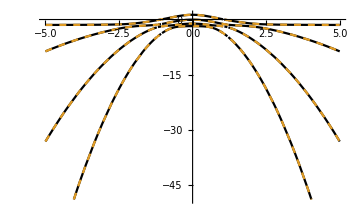
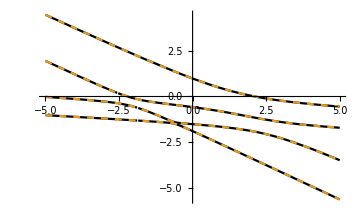

```mathematica
enCompare={PlotStyle->{Black,Dashed},ImageSize->Medium,PlotPoints->10};
{Plot[{Re@enSim[1,χ],Sort@Eigenvalues[H[1,χ]]},{χ,-5,5},Evaluate@enCompare],Plot[{Re@enSim[λ,0.8],Sort@Eigenvalues[H[λ,0.8]]},{λ,-5,5},Evaluate@enCompare]}
```

### Divergence

Crossing E_0 with E_1 for 1/2 √(enD[λ,χ]-enE[λ,χ])=0

```mathematica
FindInstance[enD[λ,χ]==enE[λ,χ],{λ,χ},Reals]
```

{{λ→-1/2,χ→√(3/5)}}

```mathematica
FindInstance[enD[λ,χ]==enE[λ,χ],{λ,χ}]
```

$Aborted

### Phase transitions

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

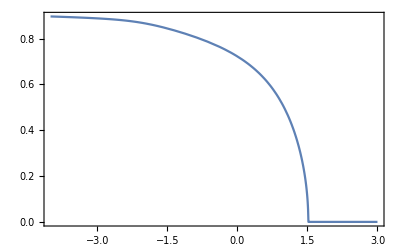

```mathematica
Plot[χ/.Last@FindMaximum[enSim[λ,χ]⟦1⟧-enSim[λ,χ]⟦2⟧,{χ,1}],{λ,-4,3},Evaluate@font,PlotPoints->30,Frame->True]
```

## Eigenvectors

```mathematica
Eigenvectors[H[λ,χ],Quartics->True]
```

```mathematica
eigA[λ_,χ_]:=16 2^(1/3) (25515+64 λ^6-108621 χ^2-192 λ^5 χ^2+309096 χ^4-326727 χ^6+162648 χ^8-81855 χ^10+24013 χ^12-8 λ^3 χ^2 (-513+414 χ^2+29 χ^4)+24 λ^4 (36-93 χ^2+52 χ^4)+6 λ χ^2 (16119-42660 χ^2+29691 χ^4-3198 χ^6+409 χ^8)+6 λ^2 (1377-10557 χ^2+17595 χ^4-10053 χ^6+1225 χ^8)+√(-(1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8)^3+(25515+8262 λ^2+864 λ^4+64 λ^6-3 (36207+2 λ (-16119+λ (10557+4 λ (-171+λ (93+8 λ))))) χ^2+6 (51516+λ (-42660+λ (17595+8 λ (-69+26 λ)))) χ^4-(326727+2 λ (-89073+λ (30159+116 λ))) χ^6+6 (27108+λ (-3198+1225 λ)) χ^8+3 (-27285+818 λ) χ^10+24013 χ^12)^2))^(1/3)
eigB[λ_,χ_]:=1/(√6)(√(2^(2/3) eigA[λ,χ]+32 (45+4 λ^2-(33+4 λ) χ^2+49 χ^4)+1/eigA[λ,χ] 512 2^(1/3) (1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8)))
eigC[λ_,χ_]:=1/(√6)(√(-2^(2/3) eigA[λ,χ]-1/eigA[λ,χ] 512 2^(1/3) (1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8)+64 (45+4 λ^2-(33+4 λ) χ^2+49 χ^4-(216 (λ-4 (-1+λ) χ^2+(-1+λ) χ^4-2 χ^6))/eigB[λ,χ])))
eigD[λ_,χ_]:=1/(√6)(√(-2^(2/3) eigA[λ,χ]-1/eigA[λ,χ] 512 2^(1/3) (1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8)+64 (45+4 λ^2-(33+4 λ) χ^2+49 χ^4+(216 (λ-4 (-1+λ) χ^2+(-1+λ) χ^4-2 χ^6))/eigB[λ,χ])))
eigE[λ_,χ_]:=(9+2 λ (9+2 λ)+57 χ^2-22 λ χ^2+49 χ^4)
eigF[λ_,χ_]:=(-81-9 λ+4 λ^3-3 (-54+λ (53+4 λ)) χ^2+3 (-74+13 λ) χ^4+55 χ^6)
```

eigC, eigD differ only in the sign at the end, assign new symbol with \pm

```mathematica
eigenVec[λ_,χ_]:={{((eigB [λ,χ])^3+(eigC [λ,χ])^3-4 (eigC [λ,χ])^2 (-9+λ+7 χ^2)-16 eigC [λ,χ] eigE[λ,χ]+64 eigF[λ,χ]+(eigB [λ,χ])^2 (3 eigC [λ,χ]-4 (-9+λ+7 χ^2))+eigB [λ,χ] (3 (eigC [λ,χ])^2-8 eigC [λ,χ] (-9+λ+7 χ^2)-16 eigE[λ,χ]))/(288 ((-8+eigB [λ,χ]+eigC [λ,χ]) λ χ+4 (5+4 λ) χ^3)),(432+48 eigB [λ,χ]+(eigB [λ,χ])^2+48 eigC [λ,χ]+2 eigB [λ,χ] eigC [λ,χ]+(eigC [λ,χ])^2+768 λ+24 eigB [λ,χ] λ+24 eigC [λ,χ] λ+320 λ^2-16 (3 (39+eigB [λ,χ]+eigC [λ,χ])+56 λ) χ^2+176 χ^4)/(24 √3 ((-8+eigB [λ,χ]+eigC [λ,χ]) λ+4 (5+4 λ) χ^2)),(λ (-432+(eigB [λ,χ])^2+24 eigC [λ,χ]+(eigC [λ,χ])^2+2 eigB [λ,χ] (12+eigC [λ,χ])-64 λ (3+λ))+8 (3 (36+eigB [λ,χ]+eigC [λ,χ])-3 (-66+eigB [λ,χ]+eigC [λ,χ]) λ+32 λ^2) χ^2-176 (6+5 λ) χ^4)/(24 √3 ((-8+eigB [λ,χ]+eigC [λ,χ]) λ χ+4 (5+4 λ) χ^3)),1},{((eigB [λ,χ])^3-(eigC [λ,χ])^3-4 (eigC [λ,χ])^2 (-9+λ+7 χ^2)+16 eigC [λ,χ] eigE[λ,χ]+64 eigF[λ,χ]-(eigB [λ,χ])^2 (3 eigC [λ,χ]+4 (-9+λ+7 χ^2))+eigB [λ,χ] (3 (eigC [λ,χ])^2+8 eigC [λ,χ] (-9+λ+7 χ^2)-16 eigE[λ,χ]))/(288 ((-8+eigB [λ,χ]-eigC [λ,χ]) λ χ+4 (5+4 λ) χ^3)),((eigB [λ,χ])^2+(eigC [λ,χ])^2-24 eigC [λ,χ] (2+λ-2 χ^2)+16 (27+48 λ+20 λ^2-(117+56 λ) χ^2+11 χ^4)-2 eigB [λ,χ] (eigC [λ,χ]-12 (2+λ-2 χ^2)))/(24 √3 ((-8+eigB [λ,χ]-eigC [λ,χ]) λ+4 (5+4 λ) χ^2)),(λ (eigB [λ,χ] (24+eigB [λ,χ])-2 eigB [λ,χ] eigC [λ,χ]+(eigC [λ,χ])^2-8 (54+3 eigC [λ,χ]+8 λ (3+λ)))+8 (3 (36+eigB [λ,χ]-eigC [λ,χ])+3 (66-eigB [λ,χ]+eigC [λ,χ]) λ+32 λ^2) χ^2-176 (6+5 λ) χ^4)/(24 √3 ((-8+eigB [λ,χ]-eigC [λ,χ]) λ χ+4 (5+4 λ) χ^3)),1},{(-(eigB [λ,χ])^3+(eigD [λ,χ])^3-4 (eigD [λ,χ])^2 (-9+λ+7 χ^2)-16 eigD [λ,χ] eigE[λ,χ]+64 eigF[λ,χ]+(eigB [λ,χ])^2 (3 eigD [λ,χ]-4 (-9+λ+7 χ^2))+eigB [λ,χ] (-3 (eigD [λ,χ])^2+8 eigD [λ,χ] (-9+λ+7 χ^2)+16 eigE[λ,χ]))/(288 ((-8-eigB [λ,χ]+eigD [λ,χ]) λ χ+4 (5+4 λ) χ^3)),((eigB [λ,χ])^2+(eigD [λ,χ])^2+24 eigD [λ,χ] (2+λ-2 χ^2)+16 (27+48 λ+20 λ^2-(117+56 λ) χ^2+11 χ^4)-2 eigB [λ,χ] (eigD [λ,χ]+12 (2+λ-2 χ^2)))/(24 √3 ((-8-eigB [λ,χ]+eigD [λ,χ]) λ+4 (5+4 λ) χ^2)),(λ (-432+(eigB [λ,χ])^2+24 eigD [λ,χ]+(eigD [λ,χ])^2-2 eigB [λ,χ] (12+eigD [λ,χ])-64 λ (3+λ))+8 (3 (36-eigB [λ,χ]+eigD [λ,χ])+3 (66+eigB [λ,χ]-eigD [λ,χ]) λ+32 λ^2) χ^2-176 (6+5 λ) χ^4)/(24 √3 ((-8-eigB [λ,χ]+eigD [λ,χ]) λ χ+4 (5+4 λ) χ^3)),1},{-(((eigB [λ,χ])^3+(eigD [λ,χ])^3+4 (eigD [λ,χ])^2 (-9+λ+7 χ^2)-16 eigD [λ,χ] eigE[λ,χ]-64 eigF[λ,χ]+(eigB [λ,χ])^2 (3 eigD [λ,χ]+4 (-9+λ+7 χ^2))+eigB [λ,χ] (3 (eigD [λ,χ])^2+8 eigD [λ,χ] (-9+λ+7 χ^2)-16 eigE[λ,χ]))/(288 (-(8+eigB [λ,χ]+eigD [λ,χ]) λ χ+4 (5+4 λ) χ^3))),-(((eigB [λ,χ])^2+(eigD [λ,χ])^2-24 eigD [λ,χ] (2+λ-2 χ^2)+16 (27+48 λ+20 λ^2-(117+56 λ) χ^2+11 χ^4)+2 eigB [λ,χ] (eigD [λ,χ]-12 (2+λ-2 χ^2)))/(24 √3 ((8+eigB [λ,χ]+eigD [λ,χ]) λ-4 (5+4 λ) χ^2))),(λ ((eigB [λ,χ])^2+2 eigB [λ,χ] (-12+eigD [λ,χ])+(eigD [λ,χ])^2-8 (54+3 eigD [λ,χ]+8 λ (3+λ)))+8 (-3 (-36+eigB [λ,χ]+eigD [λ,χ])+3 (66+eigB [λ,χ]+eigD [λ,χ]) λ+32 λ^2) χ^2-176 (6+5 λ) χ^4)/(24 √3 (-(8+eigB [λ,χ]+eigD [λ,χ]) λ χ+4 (5+4 λ) χ^3)),1}}
```

```mathematica
N@eigenVec[1,1]//TableForm
N@Eigenvectors[H[1,1]]//TableForm
```

0.291934+5.8101×10^-17 ⅈ | 0.694333+7.35711×10^-18 ⅈ | 1.06954+6.036×10^-18 ⅈ | 1.
-2.48418+1.80237×10^-16 ⅈ | -0.659472-7.79491×10^-17 ⅈ | 0.171205-3.46316×10^-17 ⅈ | 1.
0.838122-6.91709×10^-16 ⅈ | -1.66268+1.88354×10^-16 ⅈ | -0.0843572+1.72713×10^-17 ⅈ | 1.
0.109682+3.21229×10^-16 ⅈ | 0.729718-7.00792×10^-17 ⅈ | -1.43865+1.78784×10^-18 ⅈ | 1.

0.291934 | 0.694333 | 1.06954 | 1.
-2.48418 | -0.659472 | 0.171205 | 1.
0.838122 | -1.66268 | -0.0843572 | 1.
0.109682 | 0.729718 | -1.43865 | 1.

## Metric tensor

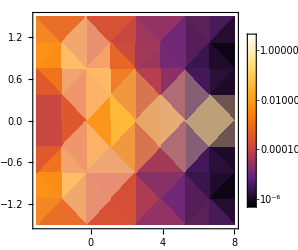

```mathematica
densA=DensityPlot[Det@gC[λ,χ],{λ,-3,8},{χ,-1.5,1.5},PlotPoints->3,PerformanceGoal->"Quality", ImageSize->250,Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotLegends->Automatic]
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_gDivergence.pdf",densA,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
gSizeDef=560;
gSize={ImageSize->{gSizeDef,gSizeDef/1.6},AspectRatio->1/2};
g11A=DensityPlot[ArcTan@gC[λ,χ]⟦1,1⟧,{λ,-3,8},{χ,-1.55,1.55},PlotPoints->300, Evaluate@densityPlotOptions,Evaluate@gSize];
g12A=DensityPlot[ArcTan@gC[λ,χ]⟦1,2⟧,{λ,-3,8},{χ,-1.55,1.55},PlotPoints->300,Evaluate@densityPlotOptions,Evaluate@gSize];
g22A=DensityPlot[ArcTan@gC[λ,χ]⟦2,2⟧,{λ,-3,8},{χ,-1.55,1.55},PlotPoints->300,Evaluate@densityPlotOptions,Evaluate@gSize];
gComponents=plotGrid[{{g11A},{g12A},{g22A}},gSizeDef,gSizeDef*2.4/1.6,ImagePadding->45]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_gComponents.pdf",gComponents,"AllowRasterization"->True,ImageResolution->800];
```

## Derivative precision

```mathematica
derPiece[λ_,χ_]=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(1+(λ+1/2)^2+(Abs[χ]-√(3/5))^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
```

```mathematica
Plot3D[derPiece[λ,χ],{λ,-6,6},{χ,-3,3},PlotLegends->Automatic,PlotPoints->10,PlotRange->All,ColorFunction->"SunsetColors"]
```

-Graphics3D-

## Christoffel symbols

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

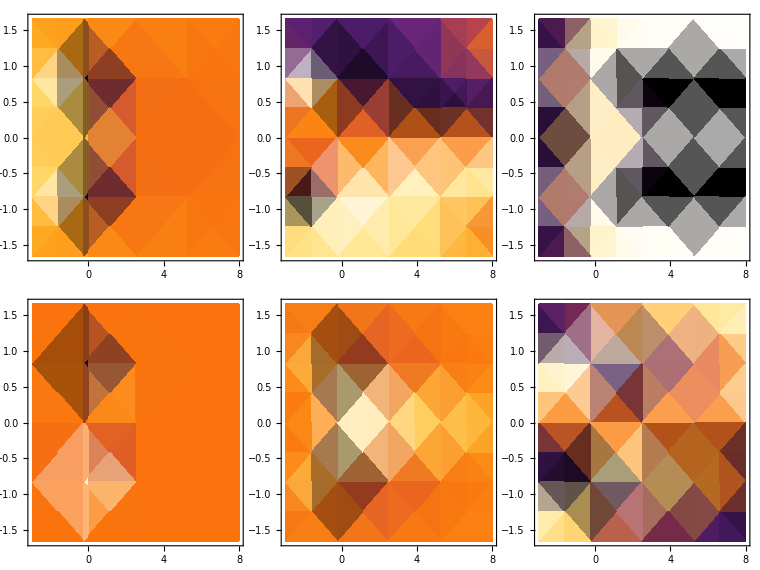

```mathematica
{gammasDen111,gammasDen121,gammasDen122}=DensityPlot[ArcTan@G1[λ,χ]⟦#⟧,{λ,-3,8},{χ,-1.65,1.65},ImageSize->190,PlotPoints->300,Evaluate@densityPlotOptions]&/@{1,2,3};
{gammasDen211,gammasDen221,gammasDen222}=DensityPlot[ArcTan@G2[λ,χ]⟦#⟧,{λ,-3,8},{χ,-1.65,1.65},ImageSize->190,PlotPoints->300,Evaluate@densityPlotOptions]&/@{1,2,3};
gammas=plotGrid[{{gammasDen111,gammasDen121,gammasDen122},{gammasDen211,gammasDen221,gammasDen222}},190*4,190*3,ImagePadding->45]
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_gammas.pdf",gammas,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
barA=BarLegend[{"SunsetColors",{-π/2,π/2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->500]
Export[NotebookDirectory[]<>"../dp_text/img/N=3_barA.pdf",barA,"AllowRasterization"->True,ImageResolution->800];
```

## Ricci and Riemann

### Basic formula

```mathematica
Ric[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,g1,g2},
derTerms=derPiece[λ,χ];
g1=G1[λ,χ];
g2=G2[λ,χ];
2/(gC[λ,χ]⟦2,2⟧)(ND[G1[l,χ],l,λ,Terms->derTerms]⟦3⟧-ND[G1[λ,c],c,χ,Terms->derTerms]⟦2⟧+g1⟦1⟧g1⟦3⟧+g1⟦2⟧g2⟦3⟧-g1⟦2⟧^2-g1⟦3⟧g2⟦2⟧)
]
```

### Ricci formula 2x2

Ricci scalar for metric 2x2 is numerically unstable around singularity

```mathematica
R1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g,l,c,dg1,dg2,R12},
derTerms=8;
g=gC[λ,χ];
dg1=ND[gC[l,χ],l,λ,Terms->derTerms];
dg2=ND[gC[λ,c],c,χ,Terms->derTerms];
1/(√Det[g])(g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
];
R2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g,l,c,dg1,dg2,R12},
derTerms=8;
g=gC[λ,χ];
dg1=ND[gC[l,χ],l,λ,Terms->derTerms];
dg2=ND[gC[λ,c],c,χ,Terms->derTerms];
1/(√Det[g])(2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
];
Ric2x2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,l,c,g},
derTerms=8;
g=gC[λ,χ];
1/(√Det[g])(ND[R1[l,χ],l,λ,Terms->derTerms]+ND[R2[λ,c],c,χ,Terms->derTerms])]
```

### Ricci plotting time

FittedModel[-571.602+218.42 x+14.2402 x^2]

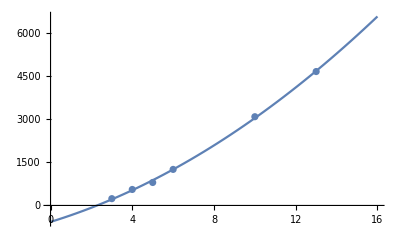

{{163673.,45.4647}}

```mathematica
ricciSpeedData={{3,236.3},{4,555.6},{5,798},{6,1253},{10,3084},{13,4654}};
RicciPlotRime=NonlinearModelFit[ricciSpeedData,a x+b x^2+c,{a,b,c},x]
Show[Plot[RicciPlotRime[x],{x,0,16}],ListPlot[ricciSpeedData]]
{#,#/3600}&/@{RicciPlotRime[100]}
```

### Plotting Ricci

```mathematica
plRic=Timing@DensityPlot[ArcTan[Ric[λ,χ]],{λ,-1,2},{χ,-1.3,1.3},PlotPoints->100,Evaluate@density3]
```

$Aborted

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_Ricci_200.pdf",plRic[[2]],"AllowRasterization"->True,ImageResolution->800];
```

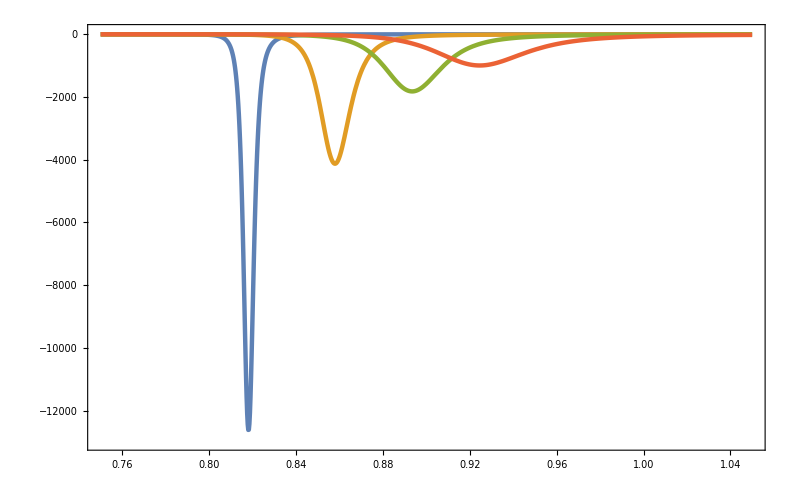

```mathematica
plRicS=Plot[{Ric[0,χ],Ric[0.5,χ],Ric[1,χ],Ric[1.5,χ]},{χ,0.75,1.05},Evaluate@plot2,FrameLabel->MaTeX/@{"\\chi","Ric"},PlotRange->{-13000,50},PlotPoints->20,PlotLegends->Placed[MaTeX/@{"\\lambda=0.0","\\lambda=0.5","\\lambda=1.0","\\lambda=1.5"},{0.8,0.2}]]
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_Ricci_section.pdf",plRicS,"AllowRasterization"->True,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
Timing@NMinimize[{Ric[1,χ],0.75<χ<1.1},{χ}]
```

{550.686,{-1819.33,{χ→0.893453}}}

### RicMinimas data and calculate

```mathematica
RicMinimas=Quiet@ParallelTable[NMinimize[{Ric[j,χ],0.7<χ<0.8},{χ}],{j,-2,0,0.1}]
```

{{-130.322,{χ→0.74948}},{-134.493,{χ→0.749431}},{-138.93,{χ→0.749484}},{-143.654,{χ→0.749671}},{-148.688,{χ→0.750034}},{-154.046,{χ→0.750583}},{-159.748,{χ→0.751408}},{-165.787,{χ→0.752468}},{-172.175,{χ→0.753612}},{-178.825,{χ→0.755357}},{-185.761,{χ→0.757623}},{-193.019,{χ→0.760109}},{-199.689,{χ→0.762996}},{-209.432,{χ→0.766626}},{-216.771,{χ→0.770353}},{-9.59848×10^15,{χ→0.774078}},{-267.925,{χ→0.741536}},{-29106.,{χ→0.792399}},{-13163.,{χ→0.799999}},{-93.3756,{χ→0.799992}},{-16.4465,{χ→0.8}}}

### Minimas Data

```mathematica
RicMinimas={{-41.13519411554519,{χ->0.7876825858705193}},{-42.3296681110105,{χ->0.7863848868098238}},{-43.657902270704845,{χ->0.7848500862770952}},{-45.14226419795752,{χ->0.7833247658881307}},{-46.81039639857656,{χ->0.7815996671711344}},{-48.696352549794604,{χ->0.7797467038051981}},{-50.84269525596393,{χ->0.7778433901885958}},{-53.30294350776076,{χ->0.7757393404330635}},{-56.14515452932515,{χ->0.7735485552172277}},{-59.45664244750929,{χ->0.7711555752159187}},{-63.35059923783233,{χ->0.7686285661209125}},{-67.97511462535597,{χ->0.765919320072939}},{-73.72158229071144,{χ->0.7627389577744922}},{-80.51499897146115,{χ->0.7597194979832318}},{-88.88906981265689,{χ->0.7566273081395515}},{-99.37703553830917,{χ->0.7536231109464759}},{-112.77608875615422,{χ->0.7509813360483828}},{-130.3036897252213,{χ->0.7500000067830356}},{-154.04613033568597,{χ->0.7505765722394073}},{-185.7498034927896,{χ->0.7573236897481422}},{-10.187053945275235,{χ->0.7500736846348174}},{-12640.104185787235,{χ->0.8180891742089713}},{-4125.407201294193,{χ->0.8579143338009999}},{-1819.3258501327336,{χ->0.8934525259423326}},{-992.2919852048701,{χ->0.9245450936806644}},{-625.6367955184811,{χ->0.9515037224726332}},{-437.49399816196154,{χ->0.9747003200155286}},{-328.81210474900456,{χ->0.9947521893166077}},{-260.63466814478824,{χ->1.0121316262650233}},{-214.80071547543707,{χ->1.0271564605067531}},{-182.88782633378352,{χ->1.0401043890950037}},{-159.52413340830896,{χ->1.0513072120315008}},{-141.87057421325963,{χ->1.0610388684102832}},{-128.18305331405878,{χ->1.069491806033852}},{-117.34331537001587,{χ->1.0768074948347774}},{-108.60655290661165,{χ->1.0830412891579626}},{-101.4614602518964,{χ->1.0883704477692262}},{-95.54664961408008,{χ->1.0926845541903918}},{-90.60076398628634,{χ->1.0965610535532413}},{-86.43050004626528,{χ->1.0997464446419356}},{-82.89051373702073,{χ->1.102497241053326}},{-79.8688946732429,{χ->1.1044515378210062}},{-77.27836163655303,{χ->1.106234175692398}},{-75.04985723348148,{χ->1.1074886393383854}},{-73.1296224269884,{χ->1.1086806339185733}},{-71.47161330027573,{χ->1.1091272376514996}},{-70.04006766703591,{χ->1.1096632610532657}},{-68.80444150063892,{χ->1.1098037532667462}},{-67.73995572804897,{χ->1.110211440938754}},{-66.82520207419245,{χ->1.110343990538068}},{-66.04181456929989,{χ->1.10985474292047}},{-65.37636551202966,{χ->1.1095303271265327}},{-64.81243245230606,{χ->1.1094404962080124}},{-64.34167241066247,{χ->1.109055225419178}},{-63.95280449884587,{χ->1.1087680191863398}},{-63.63886817036448,{χ->1.108268028340766}},{-63.39281200774231,{χ->1.107395800240252}},{-63.20280211639651,{χ->1.1067974632521416}},{-63.07048089163043,{χ->1.1063685093236761}},{-62.98685952031669,{χ->1.1064362151518399}},{-62.94608509827262,{χ->1.1059271083121474}},{-62.947417380433585,{χ->1.1047753544472907}}};
```

```mathematica
RicMinimasZoom={{-130.32232079220165,{χ->0.7494799614748978}},{-134.49331979851712,{χ->0.7494307446364674}},{-138.93036304482146,{χ->0.7494837370546791}},{-143.65416714431993,{χ->0.7496714707236629}},{-148.68763244593026,{χ->0.7500338680593501}},{-154.04551270048842,{χ->0.7505829220468256}},{-159.74787766154333,{χ->0.7514079322002656}},{-165.7874580099688,{χ->0.7524683442893407}},{-172.17458343874625,{χ->0.7536121144870139}},{-178.8246190877049,{χ->0.7553573646527988}},{-185.76139265257598,{χ->0.7576233288377315}},{-193.01852867692642,{χ->0.7601089156246282}},{-199.688508631717,{χ->0.7629955115311863}},{-209.43205767132258,{χ->0.7666259358279887}},{-216.77058656603458,{χ->0.770353053502645}},{-9.598477992228724*^15,{χ->0.7740778701793268}},{-267.9247345874587,{χ->0.7415363621053267}},{-29106.024852992738,{χ->0.7923985263884594}},{-13163.007771256609,{χ->0.7999989333747245}},{-93.3755921521559,{χ->0.7999923654296236}},{-16.446507875490543,{χ->0.7999997244494542}}};
```

### RicMinimas plot

```mathematica
plRicMinimas=ListLinePlot[Transpose@{Range[-10.5,20,0.5],χ/.Map[Last,RicMinimas]},Evaluate@plot2,FrameLabel->MaTeX/@{"\\lambda","\\chi"}];
```

```mathematica
Show[{densA,plRicMinimas}]
```

-Graphics-

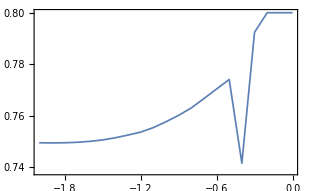

```mathematica
plRicMinimas=ListLinePlot[Transpose@{Range[-2,0,0.1],χ/.Map[Last,RicMinimasZoom]},Evaluate@plot2,FrameLabel->MaTeX/@{"\\lambda","\\chi"}]
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_RicMinimas.pdf",plRicMinimas,"AllowRasterization"->True,"AllowRasterization"->True,ImageResolution->800];
```

## Killing Field

Lie derivative kills metric, therefore metric is constant along killing field lines.

```mathematica
ND[ND[gC[l,c],l,1],c,1]
```

{{0.0456678,-0.604564},{-0.604564,4.05768}}

```mathematica
geodbg=ContourPlot[ND[ND[gC[l,c],l,λ],c,χ]==0,{λ,-3,4},{χ,-2,2},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->30,ContourStyle->{Red,Thickness[0.004]},ContourShading->None]
```

-Graphics-

## Geodesics

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-1,0},{χ,0.5,1},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->80];
```

```mathematica
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
```

### Boundary value problem

```mathematica
tmax=500;
dirichlet[i1_,i2_,f1_,f2_]:={λ[0]==i1,χ[0]==i2,λ[tmax]==f1,χ[tmax]==f2};
```

```mathematica
(*WorkingPrecision->20,Method->"StiffnessSwitching"*)
```

```mathematica
sol=NDSolve[Join[eq,dirichlet[0,0,1.2,0.6]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

```mathematica
solM=Quiet@Table[NDSolve[Join[eq,dirichlet[li,xi,-1/2,√(3/5)]],{λ,χ},{t,0,tmax},PrecisionGoal->4,AccuracyGoal->4,Method->"ExplicitRungeKutta",WorkingPrecision->150],{li,-3,4,0.5},{xi,-2,2,0.5}]
```

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.sol,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodBoundary}]
```

```mathematica
accuracy goal=4, WorkingPrecision=150,init=(li,xi,-1/2,√(3/5))  
-Graphics-
```

### Initial value problem

WorkingPrecision = 70 houd be enough (50 was same as 150)

```mathematica
tmax=15;
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
direc=Normalize@{0.4-1,0.85-0.9};
solM2=ParallelTable[NDSolve[Join[eq,cauchy[0,i,direc⟦1⟧,direc⟦2⟧]],{λ,χ},{t,0,tmax},PrecisionGoal->4,AccuracyGoal->4,WorkingPrecision->70],{i,0.81,0.83,0.005}]
```

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.solM2,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodBoundary}]
```

-Graphics-

```mathematica
solMulti1=Quiet@Table[NDSolve[Join[eq,cauchy[-1,i,0.1,0]],{λ,χ},{t,0,10},PrecisionGoal->5,AccuracyGoal->5,WorkingPrecision->170],{i,0.72,0.85,0.01}];
```

```mathematica
accuracy goal=5, WorkingPrecision=170,init=(-1,i,0.1,0)
-Graphics-
```

## Fidelity minimalization

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-1,1},{χ,0,1},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->50];
```

```mathematica
dg111[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,l},
derTerms=derPieceC[λ,χ];
ND[gC[l,χ],l,λ,Terms->derTerms]⟦1,1⟧
]
dg112[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,l},
derTerms=derPieceC[λ,χ];
ND[gC[l,χ],l,λ,Terms->derTerms]⟦1,2⟧
]
dg122[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,l},
derTerms=derPieceC[λ,χ];
ND[gC[l,χ],l,λ,Terms->derTerms]⟦2,2⟧
]
dg211[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c},
derTerms=derPieceC[λ,χ];
ND[gC[λ,c],c,χ,Terms->derTerms]⟦1,1⟧
]
dg212[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c},
derTerms=derPieceC[λ,χ];
ND[gC[λ,c],c,χ,Terms->derTerms]⟦1,2⟧
]
dg222[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c},
derTerms=derPieceC[λ,χ];
ND[gC[λ,c],c,χ,Terms->derTerms]⟦2,2⟧
]
```

```mathematica
eqF={
dg111[λ[t],χ[t]] λ'[t]^2+2dg112[λ[t],χ[t]]λ'[t]χ'[t]+dg122[λ[t],χ[t]] χ'[t]^2-2{1,0}.gC[λ[t],χ[t]].{λ''[t],0}-2{1,0}.gC[λ[t],χ[t]].{0,χ''[t]}==0,
dg211[λ[t],χ[t]] λ'[t]^2+2dg212[λ[t],χ[t]]λ'[t]χ'[t]+dg222[λ[t],χ[t]] χ'[t]^2-2{0,1}.gC[λ[t],χ[t]].{0,χ''[t]}-2{1,0}.gC[λ[t],χ[t]].{0,λ''[t]}==0
};
```

### Initial value problem

WorkingPrecision = 70 houd be enough (50 was same as 150)

```mathematica
tmax=3;
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
solGeod=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2],{i,0,0.7,0.1}]
```

{{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
sol=ParallelTable[NDSolve[Join[eqF,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2],{i,0,0.7,0.1}]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

NDSolve::ndsz: At t == 1.91737, step size is effectively zero; singularity or stiff system suspected.

{{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
geod=ParametricPlot[{λ[t],χ[t]}/.solGeod,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Blue];
fidel=ParametricPlot[{λ[t],χ[t]}/.sol,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geod,fidel}]
```

-Graphics-

## Plotting initial value geodesics

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-1.8,1},{χ,0,1},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->100];
```

```mathematica
geodInitial=Import[NotebookDirectory[]<>"savedData/solMulti_N=3_maxtheta=0,63.m"];
```

```mathematica
geodInitial1=Import[NotebookDirectory[]<>"savedData/solMulti_N=3_part1_mintheta=pi-0,205.m"];
geodInitial2=Import[NotebookDirectory[]<>"savedData/solMulti_N=3_part2_mintheta=pi-0,220.m"];
geodInitial3=Import[NotebookDirectory[]<>"savedData/solMulti_N=3_part3_mintheta=pi-0,225.m"];
geodInitial4=Import[NotebookDirectory[]<>"savedData/solMulti_N=3_part4_mintheta=pi-0,229.m"];
```

```mathematica
parametricOptions={PlotRange->All,Frame->True,PlotStyle->{Green,Thickness[0.003]}};
```

```mathematica
pl11=ParametricPlot[{λ[t],χ[t]}/.geodInitial⟦56;;64⟧,{t,0,7},Evaluate@parametricOptions];
pl12=ParametricPlot[{λ[t],χ[t]}/.geodInitial⟦1;;55⟧,{t,0,5},Evaluate@parametricOptions];
pl21=ParametricPlot[{λ[t],-χ[t]}/.geodInitial⟦56;;64⟧,{t,0,7},Evaluate@parametricOptions];
pl22=ParametricPlot[{λ[t],-χ[t]}/.geodInitial⟦1;;55⟧,{t,0,5},Evaluate@parametricOptions];
```

```mathematica
pl31=ParametricPlot[{λ[t],χ[t]}/.geodInitial1,{t,0,3},Evaluate@parametricOptions];
pl32=ParametricPlot[{λ[t],χ[t]}/.geodInitial2,{t,0,12},Evaluate@parametricOptions];
pl33=ParametricPlot[{λ[t],χ[t]}/.geodInitial3,{t,0,15},Evaluate@parametricOptions];
pl34=ParametricPlot[{λ[t],χ[t]}/.geodInitial4,{t,0,15},Evaluate@parametricOptions];
pl231=ParametricPlot[{λ[t],-χ[t]}/.geodInitial1,{t,0,3},Evaluate@parametricOptions];
pl232=ParametricPlot[{λ[t],-χ[t]}/.geodInitial2,{t,0,12},Evaluate@parametricOptions];
pl233=ParametricPlot[{λ[t],-χ[t]}/.geodInitial3,{t,0,15},Evaluate@parametricOptions];pl234=ParametricPlot[{λ[t],-χ[t]}/.geodInitial4,{t,0,15},Evaluate@parametricOptions];
```

```mathematica
plt=Show[{geodbg,pl11,pl12,pl21,pl22,pl31,pl32,pl33,pl231,pl232,pl233}, ImageSize->310]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_geodesics.pdf",plt,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
geodleft=Import[NotebookDirectory[]<>"savedData/solMulti_N=3_lambdaIn=-1.m"];
plL1=ParametricPlot[{λ[t],χ[t]}/.geodleft⟦1;;19⟧,{t,0,7},Evaluate@parametricOptions];
plL2=ParametricPlot[{λ[t],χ[t]}/.geodleft⟦22;;31⟧,{t,0,7},Evaluate@parametricOptions];
pltL=Show[{geodbg,plL1,plL2}, ImageSize->310]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_geodesics_lambdaIn=-1.pdf",pltL,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
geodB=Import[NotebookDirectory[]<>"savedData/solMulti_N=3_thetaIn=0.m"];
plB=ParametricPlot[{λ[t],χ[t]}/.geodInitialL,{t,0,7},PlotRange->All,Frame->True,PlotStyle->Green];
pltB=Show[{geodbg,plB}, ImageSize->310]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_geodesics_thetaIn=0.pdf",pltB,"AllowRasterization"->True,ImageResolution->800]
```

## Some random statistics

### Density

```mathematica
rho[λ_,χ_,β_]:=#/Tr[#]&/@Exp[-β H[λ,χ]]
```

```mathematica
Quiet@DensityPlot[Det@rho[λ,χ,1],{λ,-30,30},{χ,-15,15},Evaluate@densityPlotOptions,PlotPoints->10,ScalingFunctions->"Log"]
```

-Graphics-

### Gibbs free energy

```mathematica
G[λ_,χ_,β_]=-1/β Log[Tr[Exp[-β H[λ,χ]]]]//FullSimplify
```

-Log[ⅇ^(1/4 β (6+λ))+ⅇ^(1/12 β (6+7 λ+4 χ^2))+ⅇ^(1/4 β (-6+λ+12 χ^2))+ⅇ^(1/12 β (-6+7 λ+16 χ^2))]/β

```mathematica
plGibbs=DensityPlot[Evaluate@D[G[λ,χ,8],{χ,2}],{λ,-5,10},{χ,-2,2},Evaluate@densityPlotOptions,PlotPoints->100];
plt=Show[{plGibbs,pl11,pl12,pl21,pl22,pl31,pl32,pl33}, ImageSize->310]
```

-Graphics-

```mathematica
Reduce[D[G[λ,χ,1],{χ,3}]==0,{χ},Reals]
```

$Aborted

```mathematica
ListPlot[{#,χ}/.Last@FindMaximum[D[G[#,χ,1],{χ,2}],{χ,1}]&/@Range[-5,10,0.1]]
```

-Graphics-

```mathematica
DensityPlot[Evaluate@D[G[λ,χ,0.4],{λ,1}],{λ,-30,30},{χ,-4,4},Evaluate@densityPlotOptions,PlotPoints->100]
```

-Graphics-

### Internal energy

```mathematica
U[λ_,χ_,β_]=G[λ,χ,β]+β D[G[λ,χ,β],β]//FullSimplify
```

-((ⅇ^(1/4 β (-6+λ)) (3 ⅇ^(3 β) (6+λ)+ⅇ^(1/3 β (6+λ+χ^2)) (6+7 λ+4 χ^2)+3 ⅇ^(3 β χ^2) (-6+λ+12 χ^2)+ⅇ^(1/3 β (3+λ+4 χ^2)) (-6+7 λ+16 χ^2)))/(12 (ⅇ^(1/4 β (6+λ))+ⅇ^(1/12 β (6+7 λ+4 χ^2))+ⅇ^(1/4 β (-6+λ+12 χ^2))+ⅇ^(1/12 β (-6+7 λ+16 χ^2)))))

```mathematica
DensityPlot[U[λ,χ,0.1],{λ,-100,150},{χ,-4,4},Evaluate@densityPlotOptions]
```

### Heat capacity

```mathematica
c[λ_,χ_,β_]=-β D[U[λ,χ,β],β]//FullSimplify
```

1/(48 (ⅇ^(1/4 β (6+λ))+ⅇ^(1/12 β (6+7 λ+4 χ^2))+ⅇ^(1/4 β (-6+λ+12 χ^2))+ⅇ^(1/12 β (-6+7 λ+16 χ^2)))^2)ⅇ^(1/4 β (-6+λ)) β ((ⅇ^(1/4 β (6+λ))+ⅇ^(1/12 β (6+7 λ+4 χ^2))+ⅇ^(1/4 β (-6+λ+12 χ^2))+ⅇ^(1/12 β (-6+7 λ+16 χ^2))) (-6+λ) (3 ⅇ^(3 β) (6+λ)+ⅇ^(1/3 β (6+λ+χ^2)) (6+7 λ+4 χ^2)+3 ⅇ^(3 β χ^2) (-6+λ+12 χ^2)+ⅇ^(1/3 β (3+λ+4 χ^2)) (-6+7 λ+16 χ^2))-1/3 ⅇ^(1/4 β (-6+λ)) (3 ⅇ^(3 β) (6+λ)+ⅇ^(1/3 β (6+λ+χ^2)) (6+7 λ+4 χ^2)+3 ⅇ^(3 β χ^2) (-6+λ+12 χ^2)+ⅇ^(1/3 β (3+λ+4 χ^2)) (-6+7 λ+16 χ^2))^2+4 (ⅇ^(1/4 β (6+λ))+ⅇ^(1/12 β (6+7 λ+4 χ^2))+ⅇ^(1/4 β (-6+λ+12 χ^2))+ⅇ^(1/12 β (-6+7 λ+16 χ^2))) (9 ⅇ^(3 β) (6+λ)+1/3 ⅇ^(1/3 β (6+λ+χ^2)) (6+λ+χ^2) (6+7 λ+4 χ^2)+9 ⅇ^(3 β χ^2) χ^2 (-6+λ+12 χ^2)+1/3 ⅇ^(1/3 β (3+λ+4 χ^2)) (3+λ+4 χ^2) (-6+7 λ+16 χ^2)))

```mathematica
plHeat=DensityPlot[c[λ,χ,0.1],{λ,-100,150},{χ,-4,4},Evaluate@densityPlotOptions, PlotLabel->"k_B C"];
plt=Show[{plHeat,pl11,pl12,pl21,pl22,pl31,pl32,pl33}, ImageSize->310]
```

-Graphics-

## Trace

```mathematica
tr=Tr[H[λ,χ]]//FullSimplify
```

1/3 (-5 λ-14 χ^2)

```mathematica
DensityPlot[Tr[H[λ,χ]],{λ,-100,150},{χ,-4,4},Evaluate@densityPlotOptions, PlotLabel->"Tr(H)"]
```

-Graphics-

```mathematica
Sum[H[λ,χ]⟦i+1,i⟧,{i,1,3}]
```

-χ-√3 χ

```mathematica
Sum[H[λ,χ]⟦i+2,i⟧,{i,1,2}]
```

-λ/(√3)

# N=100

For huge matrices compute only first few energies and check for precission {vals,vecs}=Eigensystem[s,10]

Enable more functions to be compilable, for example Inverse

```mathematica
(*Internal`CompileValues[];(*to trigger auto-load*)ClearAttributes[Internal`CompileValues,ReadProtected];
syms=DownValues[Internal`CompileValues]/.HoldPattern[Verbatim[HoldPattern][Internal`CompileValues[sym_]]:>_]:>sym;
Complement[syms,Compile`CompilerFunctions[]]*)
```

```mathematica
densityPlotOptionsExport={PerformanceGoal->"Quality",PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"}
```

## Define area for derivative precision

```mathematica
{c1,c2}={0,0};
derPiece[λ_?NumericQ,χ_?NumericQ]:=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(0.8+(λ-c1)^2+(Abs[χ]-c2)^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
Plot3D[derPiece[λ,χ],{λ,-6,6},{χ,-3,3},PlotLegends->Automatic,PlotPoints->30,PlotRange->All,ColorFunction->"SunsetColors"]
```

## Defining compiled functions

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPiece[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPiece[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

Check Christoffel symbols. If wrong, increase derTerms.

```mathematica
{gammasDen111,gammasDen121,gammasDen122}=DensityPlot[ArcTan@G1[λ,χ]⟦#⟧,{λ,-3,8},{χ,-1.5,1.5},ImageSize->190,PlotPoints->100,Evaluate@densityPlotOptionsExport]&/@{1,2,3}
```

```mathematica
{gammasDen211,gammasDen221,gammasDen222}=DensityPlot[ArcTan@G2[λ,χ]⟦#⟧,{λ,-3,8},{χ,-1.5,1.5},ImageSize->190,PlotPoints->100,Evaluate@densityPlotOptionsExport]&/@{1,2,3}
```

```mathematica
barA=BarLegend[{"SunsetColors",{-π/2,π/2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->500]
Export[NotebookDirectory[]<>"N=100_barA.pdf",barA,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
Export[NotebookDirectory[]<>"N=100_G111.pdf",gammasDen111,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"N=100_G121.pdf",gammasDen121,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"N=100_G122.pdf",gammasDen122,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
Export[NotebookDirectory[]<>"N=100_G211.pdf",gammasDen211,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"N=100_G221.pdf",gammasDen221,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"N=100_G222.pdf",gammasDen222,"AllowRasterization"->True,ImageResolution->800];
```

# N → ∞

### Phase transitions

```mathematica
en0[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort[enNonSort]⟦1⟧
]
en1[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort[enNonSort]⟦2⟧
]
```

```mathematica
transMin3=Plot[χ/.Last@FindMaximum[{en0[λ,χ]-en1[λ,χ],χ>0},{χ,1}],{λ,-5,2},Evaluate@font,PlotPoints->30,Frame->True,Axes->False,PlotStyle->{Black,Dashed,Thickness[0.004]},PlotLegends->Automatic];
```

```mathematica
transAnal=ContourPlot[χ^2==(λ-1)/(λ-2),{λ,-5,2},{χ,-0,1},ContourStyle->Red,AspectRatio->6/10];
transline=ListLinePlot[{{1,0},{5,0}},PlotStyle->{Red,Thickness[0.004]}];
transP=ListPlot[{{1,0}},PlotStyle->{Blue,PointSize[Large]}];
```

```mathematica
transCompare=Show[{transAnal,transline,transMin3,transP},ImageSize->Medium,Evaluate@font,FrameLabel->MaTeX/@{"\\lambda","\\chi"},ImageSize->410,AspectRatio->0.4]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/infiniteN_transitionCompare.pdf",transCompare,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
nn=100;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
```

Probably is Hermitean

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
Timing@gC[1,1]
```

{0.423891,{{0.672536,-4.06659},{-4.06659,24.6038}}}

## Energies

```mathematica
energies1=Eigenvalues[H[1,χ]];
energies2=Eigenvalues[H[λ,1]];
plotOpt={PlotLegends->MaTeX/@{"E_0","E_1","E_2","E_3"},PlotPoints->20,PlotRange->{Automatic,{-10,5}},Evaluate@font,ImageSize->Medium,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Frame->True,Axes->False};
{plA,plB}={Plot[energies1,{χ,-15,15},Evaluate@plotOpt],
Plot[energies2,{λ,-15,15},Evaluate@plotOpt]}
```

```mathematica
Export[NotebookDirectory[]<>"N=100_energiesl.pdf",plA,"AllowRasterization"->True,ImageSize->340,ImageResolution->800];
Export[NotebookDirectory[]<>"N=100_energiesc.pdf",plB,"AllowRasterization"->True,ImageSize->340,ImageResolution->800];
```

## Metric tensor

```mathematica
densA=DensityPlot[Det@gC[λ,χ],{λ,-3,8},{χ,-1.5,1.5},PlotPoints->100,PerformanceGoal->"Quality", ImageSize->310,Evaluate@densityPlotOptions,ScalingFunctions->"Log10"]
```

```mathematica
Export[NotebookDirectory[]<>"N=100_gDivergence.pdf",densA,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
g11A=DensityPlot[ArcTan@gC[λ,χ]⟦1,1⟧,{λ,-3,8},{χ,-1.5,1.5},PlotPoints->100, Evaluate@densityPlotOptionsExport,ImageSize->190]
g12A=DensityPlot[ArcTan@gC[λ,χ]⟦1,2⟧,{λ,-3,8},{χ,-1.5,1.5},PlotPoints->100,Evaluate@densityPlotOptionsExport,ImageSize->190]
g22A=DensityPlot[ArcTan@gC[λ,χ]⟦2,2⟧,{λ,-3,8},{χ,-1.5,1.5},PlotPoints->100,Evaluate@densityPlotOptionsExport,ImageSize->190]
```

```mathematica
Export[NotebookDirectory[]<>"N=100_g11.pdf",g11A,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"N=100_g12.pdf",g12A,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"N=100_g22.pdf",g22A,"AllowRasterization"->True,ImageResolution->800];
```

## Singularity coordinates

```mathematica
gSing={{3,-1/2,√(3/5)},{4,-0.333,0.756},{5,-0.2501,0.7454},{6,-0.2,0.738},{7,-0.173,0.7346},{8,-0.14,0.73},{9,-0.1255,0.7277},{10,-0.1111,0.7255},{11,-0.1,0.7238},{12,-0.09,0.7223},{13,-0.0834,0.7211},{14,-0.0769,0.72}};
```

```mathematica
ListPointPlot3D[gSing,Filling->Bottom]
```

-Graphics3D-

```mathematica
data23=Transpose[Transpose[gSing]⟦2;;3⟧];
model23=fa √((1-t)/(2-t));
fit23=FindFit[data23,model23,{fa},t]
```

{fa→0.99997}

```mathematica
divPosition=ListPlot[Table[Callout[Transpose[Transpose[gSing]⟦2;;3⟧]⟦i-2⟧,i],{i,3,14}],Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"\\lambda","\\chi"},ImageSize->Medium];
regr=Plot[√((1-l)/(2-l)),{l,-1,0},PlotStyle->{Gray,Thickness[0.004]}];
divPos=Show[{divPosition,regr}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/divPosition.pdf",divPos];
```

Coordinates of singularities for different nn. For nn = 3 exist only one point {3, -0.5, 0.7746}, then at least 2.

```mathematica
sing2={{4,-0.3,0.8944},{5,-1.5,0.845},{6,-1,0.865},{7,-0.7527,0.7979}};
ListPointPlot3D[sing2,Filling->Bottom]
```

-Graphics3D-

```mathematica
Hcl[x_,p_,λ_,χ_]:=-1/2+(1-λ)/2 x^2+(λ-χ^2)/4 x^4-(χ x^3)/2 √(2-x^2-p^2)-χ^2/4 p^4+p^2/4(2+(λ-2 χ^2)x^2-2χ x √(2-x^2-p^2))
DxHcl[x_,p_,λ_,χ_]= D[Hcl[x,p,λ,χ],x]//FullSimplify
DpHcl[x_,p_,λ_,χ_]= D[Hcl[x,p,λ,χ],p]//FullSimplify
```

## Separatrix

1/(2 √(2-p^2-x^2))(p^2 (-2+p^2) χ+(-6+5 p^2) x^2 χ+4 x^4 χ+2 x^3 √(2-p^2-x^2) (λ-χ^2)+x √(2-p^2-x^2) (2+(-2+p^2) λ-2 p^2 χ^2))

1/2 p (2+((-4+3 p^2) x χ)/(√(2-p^2-x^2))+(3 x^3 χ)/(√(2-p^2-x^2))-2 p^2 χ^2+x^2 (λ-2 χ^2))

```mathematica
Hcl[0,0,λ,χ]//FullSimplify
```

-1/2

```mathematica
soll=Solve[{Hcl[x,0,λ,χ]==0,DxHcl[x,0,λ,χ]==0},{λ,χ}]
```

{{λ→1/2 (3-4/x^2-(√(8-6 x^2+3 x^4))/(x √(2-x^2))),χ→(-x^3 √(2-x^2)+x^2 √(8-6 x^2+3 x^4))/(2 x^4)},{λ→1/2 (3-4/x^2+(√(8-6 x^2+3 x^4))/(x √(2-x^2))),χ→(-x^3 √(2-x^2)-x^2 √(8-6 x^2+3 x^4))/(2 x^4)}}

```mathematica
ParametricPlot[{λ,χ}/.soll,{x,0,1},PlotRange->{-10,10}]
```

-Graphics-

```mathematica
Hcl[x,0,λ,χ]
DxHcl[x,0,λ,χ]//FullSimplify
```

-1/2+1/2 x^2 (1-λ)-1/2 x^3 √(2-x^2) χ+1/4 x^4 (λ-χ^2)

x (1+(-1+x^2) λ-(x χ (3-2 x^2+x √(2-x^2) χ))/(√(2-x^2)))